# Sistemi Meccanici e Modelli Homework 3 - Anno Accademico 2022-23

## Istruzioni (aggiornate 25/10/22) Stefano Tonini 218722 stefano.tonini-2@studenti.unitn.it

### Svolgimento dell’homework

Sviluppare gli argomenti indicati  e produrre un notebook Mathematica documentato che, per ogni punto, illustri:
a) Gli elementi di teoria utilizzati.
b) Lo svolgimento e i risultati.

Indicare: nome, matricola e la e-mail.
Data di consegna dell’elaborato: una settimana prima dell’esame scelto. Comunque entro l’appello di Settembre..

### Modalità di esame

Le modalità d’esame previste nel Syllabus sono riportate di seguito:

#### Metodi didattici e attività di apprendimento richieste allo studente

(...). Si assegneranno 3 homework per lo svolgimento individuale a casa. Gli homework consistono nella risoluzione di problemi di media complessità, applicando gli elementi appresi durante il corso.
Una licenza personale di Wolfram Mathematica sarà data ad ogni studente. Durante il corso Wolfram Mathematica sarà utilizzato per creare e analizzare modelli matematici di vari sistemi meccanici con i metodi teorici indicati sopra. Mathematica sarà inoltre necessaria per lo svolgimento dei 3 homework.

(...).Three homeworks will be assigned for individual study. The homeworks consist of solving problems of medium complexity, applying the elements learned in the course.
A personal Wolfram Mathematica license will be given to each student. During the course Wolfram Mathematica will be used to create and analyze mathematical models of various mechanical systems using the theoretical methods outlined above. Mathematica will also be required for the execution of the 3 homeworks.

#### Metodo di accertamento e criteri di valutazione

L‘esame è composto di una prova scritta e dei 3 homework. 
Lo scritto è composto di una o più brevi domande di teoria e/o esercizi. Seguirà una correzione dello scritto e degli homework nella quale il docente potrà chiedere chiarimenti sugli elaborati. La correzione verrà svolta per appuntamento individualmente su Zoom.
Eventuali lacune su parti del programma non possono essere colmate rispondendo a domande aggiuntive su altre parti del programma. Qualora fosse acclarata una preparazione con lacune l’esame non può essere superato. Per esempio, costituiscono gravi lacune la incapacità di scrivere le equazioni della cinematica e della dinamica con uno dei metodi spiegati a lezione (per esempio la incapacità di scrivere ed applicare le equazioni di Newton-Eulero).
Il voto viene attribuito attraverso un giudizio complessivo sulla prova e sulla discussione degli homework svolti (tutti gli homework saranno stati corretti ma la valutazione resta riservata fino all’esame). In particolare la prova scritta vale fino a 18 punti e gli homework fino 4 punti ciascuno. E’ possibile fare l’esame senza uno o più homework, ma il voto sarà ridotto in proporzione a quanto non è stato consegnato.
Lo svolgimento degli homework, entro le scadenze assegnate, è obbligatorio.  I primi due homework hanno scadenza fissa per tutti gli studenti. L’ultimo homework potrà essere consegnato una settima prima dell’esame (e non oltre l’appello di settembre).

The examination consists of a written test and the 3 homework papers. 
The written consists of one or more short theory questions and/or exercises. This will be followed by a correction of the written part and homeworks in which the lecturer may ask for clarification of the papers. The correction will be done by appointment individually on Zoom.
Any gaps on parts of the syllabus cannot be filled by answering additional questions on other parts of the syllabus. If preparation with gaps is established, the exam cannot be passed. For example, the inability to write the equations of kinematics and dynamics by any of the methods explained in class (e.g., the inability to write and apply the Newton-Euler equations) constitute serious gaps.
The grade is awarded through an overall judgment on the proof and discussion of the homework done (all homework will have been corrected but the grade remains confidential until the exam). Specifically, the written test is worth up to 18 points and the homework up to 4 points each. It is possible to take the exam without one or more homework, but the grade will be reduced in proportion to what was not handed in.
Doing the homework, within the assigned deadlines, is mandatory. The first two homeworks have fixed deadlines for all students. The last homework may be turned in one week before the exam (and no later than the September roll call).

## Sintesi del trabucco

Si consideri il trabucco dell’homework 1. Si intende ottimizzare la gittata agendo sui parametri h, L, L1, L2, m2, L3.  La massa m2 deve essere  al massimo 12000 kg.  La massa m1 sia pari a 0.25 kg per metro di lunghezza della trave L. La massa m3 da lanciare sia m3 = 200 kg.

-Graphics-

### Si richiede:

### a) Realizzare una funzione che, simulando le due fasi del trabucco, calcola la gittata. La direzione da considerare è quella verso -x, che ha gittate maggiori. Fare attenzione che potrebbe succedere che, per alcune combinazioni di parametri, l'integrazione numerica, oppure la ricerca del tempo di rilascio, falliscano. Nella funzione controllare i risultati a ogni passo e nel caso in cui non siano validi restituire gittata zero, in modo che la ricerca della configurazione ottima si orienti automaticamente lontano da quelle configurazioni.

#### Parametri, posizioni, Equazioni N-E, Reazioni vincolari iniziali, Condizioni iniziali

```mathematica
(*Parametri*)
g=9.8;
fc=0.2;
m1=0.25L;
m3=200;
(*2 Gradi di libertà*)
θ1= q1[t];
θ2=q2[t];
(*Momento d'inerzia del corpo 1 e del corpo 2*)
I1=1/12 m1 L^2;
I2=1/12 m2 L2^2;
(*Momento d'inerzia del corpo 1 con polo A (con teorema Huygens-Steiner)*)
IA=I1+m1(L/2-L1)^2;
(*Coordinate dei punti A,B,C,D*)
xA=0;
yA=h;
xB=xA+L1 Cos[θ1];
yB=yA+L1 Sin[θ1];
xC=xA-(L-L1)Cos[θ1];
yC=yA-(L-L1)Sin[θ1];
xD=xC-L3 Cos[θ3[t]];
yD=yC-L3 Sin[θ3[t]];
(*Posizioni dei baricentri*)
xG1=xA-(L/2-L1)Cos[θ1];
yG1=yA-(L/2-L1)Sin[θ1];
xG2=xB+L2 Cos[θ2];
yG2=yB+L2 Sin[θ2];
xG3=xD;
yG3=yD;
(*Equazioni N-E per il corpo 1*)
N1x=m1*D[xG1, t,t]==-R2x-R3 Cos[θ3[t]]+R1x;
N1y=m1*D[yG1, t,t]==-R2y-R3 Sin[θ3[t]]-m1*g+R1y;
E1=IA*D[θ1, t,t]==MAR2-MARC-MAm1g;
(*Equazioni N-E per il corpo 2*)
N2x=m2*D[xG2, t,t]==R2x;
N2y=m2*D[yG2, t,t]==R2y-m2*g;
E2=I2*D[θ2, t,t]==-MG2R2;
(*Equazioni N per il corpo 3*)
N3x=m3*D[xG3, t,t]==R3 Cos[θ3[t]]-N3*fc;
N3y=m3*D[yG3, t,t]==N3+R3 Sin[θ3[t]]-m3*g;
(*Calcolo i momenti delle forze*)
AB = L1 {Cos[θ1],Sin[θ1],0};
MAR2 = (AB×{R2x,R2y,0})[[3]];

AC=(L-L1) {Cos[θ1],Sin[θ1],0};
MARC= (AC×{R3 Cos[θ3[t]],R3 Sin[θ3[t]],0})[[3]];

G2B = L2{Cos[θ2],Sin[θ2],0};
MG2R2 = (G2B ×{R2x,R2y,0})[[3]];

AG1 = (L/2-L1){Cos[θ1],Sin[θ1],0};
MAm1g =(AG1 ×{0,m1*g,0})[[3]];

(*Espressioni delle reazioni vincolari per la fase 1*)
solR=Simplify@Solve[{N1x,N1y,N2x,N2y,N3x,N3y},{R1x,R1y,R2x,R2y,R3,N3}];
Simplify@Solve[{E1,E2},{q1''[t],q2''[t]}]/.solR;
E2GdL= Simplify[{E1,E2}/.solR];
(*Condizioni iniziali della fase 1*)
Ci={q2[0]==  -π/2,q2'[0]== 0,q1[0]==π- ArcSin[h/(L-L1)],q1'[0]== 0};
```

#### Funzione Gittata

```mathematica
(*Definisco il parametro per monitorare le iterazioni*)
i=0;
```

```mathematica
Gittata[h_,L_,L1_,L2_,m2_,L3_]:= Module[
{Gopt}, 

(*Disequzione per verificare l'esistenza della configurazione iniziale*)
If[L2<h<(L-L1),
θ3[t_]:=ArcSin[(h+(-L+L1) Sin[q1[t]])/L3];
Sys=E2GdL∪Ci∪{WhenEvent[Evaluate[{N3/.solR}[[1,1]]==0],"StopIntegration"]};
sol=NDSolve[Sys,{q1,q2},{t,0,15}];
(*Istante in cui la normale del piano N3 è uguale a zero*)
T1=sol[[1,1,2,1,1,2]];
(*Condizioni finali della fase 1 che diventeranno le condizioni iniziali della fase 2*)
Cf={q1[T1],q1'[T1],q2[T1],q2'[T1],θ3[T1],θ3'[T1]}/.sol;
(*Aggiungo il terzo grado di libertà*)
θ3[t_]:=q3[t];
(*Reazione vincolare del piano uguale a zero*)
N3=0;
(*Espressioni delle reazioni vincolari per la fase 2*)
solR2=Simplify@Solve[{N1y,N1x,N2x,N2y,N3y},{R1x,R1y,R2x,R2y,R3}];
E3GdL=Simplify[{E1,E2,N3x}/.solR2];
Ci2={q1[T1]== Cf[[1,1]],q1'[T1]== Cf[[1,2]],q2[T1]== Cf[[1,3]],q2'[T1]== Cf[[1,4]],θ3[T1]==Cf[[1,5]],θ3'[T1]==Cf[[1,6]]};
Sys2=E3GdL∪Ci2∪{WhenEvent[Evaluate[{R3/.solR2}[[1,1]]==0],"StopIntegration"]};
sol2=NDSolve[Sys2,{q1,q2,q3},{t,T1,15}];
T2=sol2[[1,1,2,1,1,2]];
(*Tempo di volo*)
Tv=2(D[yG3, t])/g;
(*Gittata*)
G= (D[xG3, t])*Tv;
FG=Evaluate[G/.sol2];
(* Calocolo la gittata massima del proiettile verso destra*)
Gmax=NMaximize[{FG[[1]],T1<t<T2},t,Method->{"NelderMead","PostProcess"->False}];
Topt1=Gmax[[2,1,2]];
(* Calocolo la gittata massima del proiettile verso sinistra*)
Gmin=NMinimize[{FG[[1]],Topt1<t<T2},t,Method->{"NelderMead","PostProcess"->False}];
Gopt=Gmin[[1]];
Topt2=Gmin[[2,1,2]];
(*Aumento il parametro che conta le iterazioni*)
i++;
(*Posizioni dei punti del trabucco in funzione del tempo che utilizzo per plottare le configurazioni nella fase di lancio (fase 2)*)
xAt2[t_]:=Evaluate[xA/.sol2];
yAt2[t_]:=Evaluate[yA/.sol2];
xDt2[t_]:=Evaluate[xD/.sol2];
yDt2[t_]:=Evaluate[yD/.sol2];
xCt2[t_]:=Evaluate[xC/.sol2];
yCt2[t_]:=Evaluate[yC/.sol2];
xBt2[t_]:=Evaluate[xB/.sol2];
yBt2[t_]:=Evaluate[yB/.sol2];
xG2t2[t_]:=Evaluate[xG2/.sol2];
yG2t2[t_]:=Evaluate[yG2/.sol2];
(*Restituisce la gittata massima verso sinistra se la disequazione è verificata altrimenti restituisce 0*)
{Gopt},{0}]
]
```

```mathematica
F[h_?NumericQ,L_?NumericQ,L1_?NumericQ,L2_?NumericQ,m2_?NumericQ,L3_?NumericQ]:=Gittata[h,L,L1,L2,m2,L3][[1]]
```

#### Verifica funzione gittata

```mathematica
(*Verifica della funzione gittata inserendo i parametri dell'homework 2*)
Block[{h=10,L=20,L1=2,L2=2,m2=10000,L3=15},F[h,L,L1,L2,m2,L3]]
```

-129.85

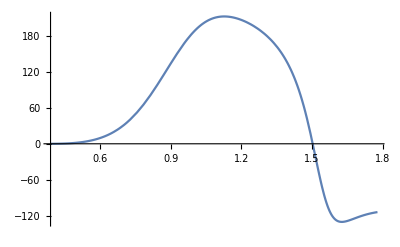

```mathematica
(*Grafico gittata con configurazione del trabucco corrisponde a quella dell'homework 2*)
Plot[FG,{t,T1,T2},PlotRange->All,GridLines->{{Topt1,Topt2},{Gmax,Gmin}},GridLinesStyle->Directive[Orange,Dashed]]
```

### b) Ottimizzare la gittata. Fare attenzione che, al variare dei parametri h, L, L1, L2, m2, L3, la configurazione iniziale esista (se necessario formulare una opportuna disequazione). Utilizzare Method→{“NelderMead”,”PostProcess”->False}.

```mathematica
i=1;
```

```mathematica
(*Numero di iterazioni "i" e valori ottenuti a quel passo di iterazione*)
Row[{"i=",Dynamic[i]," Gmax(dx)=",Dynamic[Gmax]," Gmax(sx)=",Dynamic[Gmin]," T1=",Dynamic[T1]," T2=",Dynamic[T2]}]
```

i= Gmax(dx)= Gmax(sx)= T1= T2=

```mathematica
(*Grafico che mostra le configurazione nell'istante di lancio per la gittata massima verso destra (grafico verde) e la configurazione per la gittata massima verso sinistra (grafico rosso)*)
Dynamic@Show[ListLinePlot[Block[{t=Topt1},{{xDt2[t][[1]],yDt2[t][[1]]},{xCt2[t][[1]],yCt2[t][[1]]},{xAt2[t][[1]],yAt2[t][[1]]},{xBt2[t][[1]],yBt2[t][[1]]},{xG2t2[t][[1]],yG2t2[t][[1]]}}],PlotRange->{{-10,30},{-10,40}},AspectRatio->1,PlotMarkers->{"●",10},PlotStyle->{Dashed,Green}],ListLinePlot[Block[{t=Topt2},{{xDt2[t][[1]],yDt2[t][[1]]},{xCt2[t][[1]],yCt2[t][[1]]},{xAt2[t][[1]],yAt2[t][[1]]},{xBt2[t][[1]],yBt2[t][[1]]},{xG2t2[t][[1]],yG2t2[t][[1]]}}],PlotRange->{{-10,30},{-10,40}},AspectRatio->1,PlotMarkers->{"●",10},PlotStyle->{Dashed,Red}]]
```

```mathematica
solM=NMinimize[{
F[h,L,L1,L2,m2,L3],
10<h<11,
15<L< 25,
1<L1<3,
1<L2<3,
9000<m2<12000,
10<L3<15},{h,L,L1,L2,m2,L3},Method->{"NelderMead","PostProcess"->False}]
```

NMinimize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{-556.523,{h→10.6361,L→15.0053,L1→2.9951,L2→2.88932,m2→11976.2,L3→10.3464}}

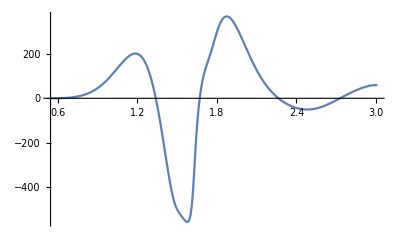

```mathematica
(*Grafico della gittata del proiettile nella configurazione appena trovata con la prima ottimizzazione*)
Plot[FG,{t,T1,T2},PlotRange->All,GridLines->{{Topt1,Topt2},{Gmax,Gmin}},GridLinesStyle->Directive[Orange,Dashed]]
```

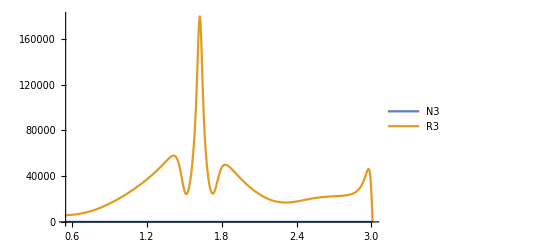

```mathematica
(*Grafico della normale del piano N3 e della tensione della fune R3*)
{h,L,L1,L2,m2,L3}={h,L,L1,L2,m2,L3}/.solM[[2]];
Plot[Evaluate[Simplify@Evaluate[{N3,R3}/.solR2]/.sol2],{t,T1,T2},PlotRange->All,PlotLegends->{"N3","R3"}]
```

```mathematica
(*Animazione che mostra le configurazione nell'istante di lancio per la gittata massima verso destra (grafico verde) e la configurazione per la gittata massima verso sinistra (grafico rosso).
In blu mostra il movimento del trabucco per quella corrispondente configurazione*)
Animate[Show[ListLinePlot[Block[{t=Topt1},{{xDt2[t][[1]],yDt2[t][[1]]},{xCt2[t][[1]],yCt2[t][[1]]},{xAt2[t][[1]],yAt2[t][[1]]},{xBt2[t][[1]],yBt2[t][[1]]},{xG2t2[t][[1]],yG2t2[t][[1]]}}],PlotRange->{{-10,30},{-10,40}},AspectRatio->1,PlotMarkers->{"●",10},PlotStyle->{Dashed,Green}],ListLinePlot[Block[{t=Topt2},{{xDt2[t][[1]],yDt2[t][[1]]},{xCt2[t][[1]],yCt2[t][[1]]},{xAt2[t][[1]],yAt2[t][[1]]},{xBt2[t][[1]],yBt2[t][[1]]},{xG2t2[t][[1]],yG2t2[t][[1]]}}],PlotRange->{{-10,30},{-10,40}},AspectRatio->1,PlotMarkers->{"●",10},PlotStyle->{Dashed,Red}],ListLinePlot[{{xDt2[t][[1]],yDt2[t][[1]]},{xCt2[t][[1]],yCt2[t][[1]]},{xAt2[t][[1]],yAt2[t][[1]]},{xBt2[t][[1]],yBt2[t][[1]]},{xG2t2[t][[1]],yG2t2[t][[1]]}},PlotRange->{{-10,30},{-10,40}},AspectRatio->1,PlotMarkers->{"●",10}]],{t,T1,T2}]
```

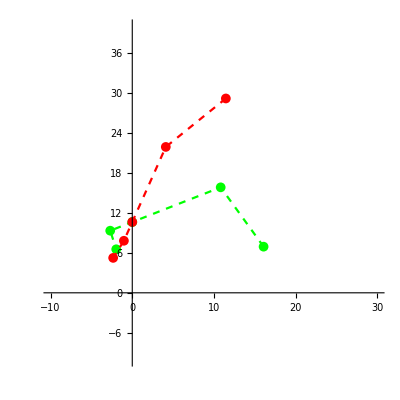

```mathematica
(*Grafico che mostra le configurazione nell'istante di lancio per la gittata massima verso destra (grafico verde) e la configurazione per la gittata massima verso sinistra (grafico rosso),dopo la prima ottimizzazione.
Questo grafico non varia con le ottimizzazioni successive*)
Show[ListLinePlot[{{xDt2[Topt1][[1]],yDt2[Topt1][[1]]},{xCt2[Topt1][[1]],yCt2[Topt1][[1]]},{xAt2[Topt1][[1]],yAt2[Topt1][[1]]},{xBt2[Topt1][[1]],yBt2[Topt1][[1]]},{xG2t2[Topt1][[1]],yG2t2[Topt1][[1]]}},PlotRange->{{-10,30},{-10,40}},AspectRatio->1,PlotMarkers->{"●",10},PlotStyle->{Dashed,Green}],ListLinePlot[{{xDt2[Topt2][[1]],yDt2[Topt2][[1]]},{xCt2[Topt2][[1]],yCt2[Topt2][[1]]},{xAt2[Topt2][[1]],yAt2[Topt2][[1]]},{xBt2[Topt2][[1]],yBt2[Topt2][[1]]},{xG2t2[Topt2][[1]],yG2t2[Topt2][[1]]}},PlotRange->{{-10,30},{-10,40}},AspectRatio->1,PlotMarkers->{"●",10},PlotStyle->{Dashed,Red}]]
```

```mathematica
(*Pulisco i parametri appena calcolati in questa ottimizzazione*)
Clear[h,L,L1,L2,m2,L3]
```

### c) Otttimizzare la gittata prendendo, inizialmente, per i parametri piccoli intervalli attorno alla configurazione dell’homework 1. Realizzare una animazione che mostra la configurazione di gittata massima durante le iterazioni di ricerca dell’ottimo e la corrispondente gittata.

#### Ottimizzazione 2

```mathematica
(*Numero di iterazioni "i" e valori ottenuti a quel passo di iterazione*)
 Row[{"i=",Dynamic[i]," Gmax(dx)=",Dynamic[Gmax]," Gmax(sx)=",Dynamic[Gmin]," T1=",Dynamic[T1]," T2=",Dynamic[T2]}]
```

i= Gmax(dx)= Gmax(sx)= T1= T2=

```mathematica
(*Grafico che mostra le configurazione nell'istante di lancio per la gittata massima verso destra (grafico verde) e la configurazione per la gittata massima verso sinistra (grafico rosso)*)
Dynamic@Show[ListLinePlot[Block[{t=Topt1},{{xDt2[t][[1]],yDt2[t][[1]]},{xCt2[t][[1]],yCt2[t][[1]]},{xAt2[t][[1]],yAt2[t][[1]]},{xBt2[t][[1]],yBt2[t][[1]]},{xG2t2[t][[1]],yG2t2[t][[1]]}}],PlotRange->{{-10,30},{-10,40}},AspectRatio->1,PlotMarkers->{"●",10},PlotStyle->{Dashed,Green}],ListLinePlot[Block[{t=Topt2},{{xDt2[t][[1]],yDt2[t][[1]]},{xCt2[t][[1]],yCt2[t][[1]]},{xAt2[t][[1]],yAt2[t][[1]]},{xBt2[t][[1]],yBt2[t][[1]]},{xG2t2[t][[1]],yG2t2[t][[1]]}}],PlotRange->{{-10,30},{-10,40}},AspectRatio->1,PlotMarkers->{"●",10},PlotStyle->{Dashed,Red}]]
```

```mathematica
solM=NMinimize[{
F[h,L,L1,L2,m2,L3],
9<h<11,
15<L< 25,
2<L1<4,
2<L2<4,
10000<m2<12000,
8<L3<12},{h,L,L1,L2,m2,L3},Method->{"NelderMead","PostProcess"->False}]
```

NMinimize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{-788.335,{h→10.941,L→15.8233,L1→3.99968,L2→3.99954,m2→12000.,L3→11.9987}}

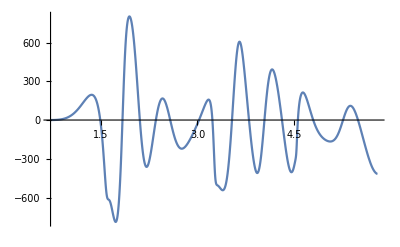

```mathematica
(*Grafico della gittata del proiettile nella configurazione appena trovata con la seconda ottimizzazione*)
Plot[FG,{t,T1,T2},PlotRange->All,GridLines->{{Topt1,Topt2},{Gmax,Gmin}},GridLinesStyle->Directive[Orange,Dashed]]
```

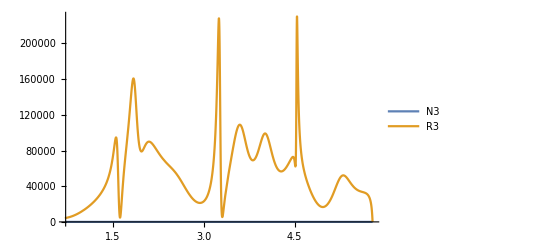

```mathematica
(*Grafico della normale del piano N3 e della tensione della fune R3*)
{h,L,L1,L2,m2,L3}={h,L,L1,L2,m2,L3}/.solM[[2]];
Plot[Evaluate[Simplify@Evaluate[{N3,R3}/.solR2]/.sol2],{t,T1,T2},PlotRange->All,PlotLegends->{"N3","R3"}]
```

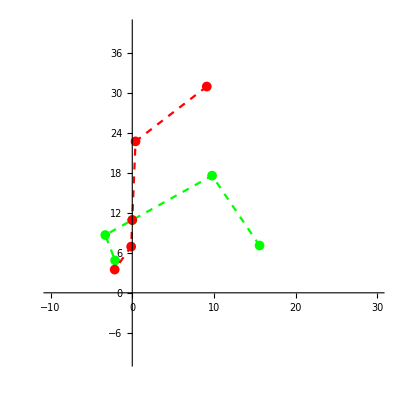

```mathematica
(*Grafico che mostra le configurazione nell'istante di lancio per la gittata massima verso destra (grafico verde) e la configurazione per la gittata massima verso sinistra (grafico rosso),dopo la seconda ottimizzazione.
Questo grafico non varia con le ottimizzazioni successive*)
Show[ListLinePlot[{{xDt2[Topt1][[1]],yDt2[Topt1][[1]]},{xCt2[Topt1][[1]],yCt2[Topt1][[1]]},{xAt2[Topt1][[1]],yAt2[Topt1][[1]]},{xBt2[Topt1][[1]],yBt2[Topt1][[1]]},{xG2t2[Topt1][[1]],yG2t2[Topt1][[1]]}},PlotRange->{{-10,30},{-10,40}},AspectRatio->1,PlotMarkers->{"●",10},PlotStyle->{Dashed,Green}],ListLinePlot[{{xDt2[Topt2][[1]],yDt2[Topt2][[1]]},{xCt2[Topt2][[1]],yCt2[Topt2][[1]]},{xAt2[Topt2][[1]],yAt2[Topt2][[1]]},{xBt2[Topt2][[1]],yBt2[Topt2][[1]]},{xG2t2[Topt2][[1]],yG2t2[Topt2][[1]]}},PlotRange->{{-10,30},{-10,40}},AspectRatio->1,PlotMarkers->{"●",10},PlotStyle->{Dashed,Red}]]
```

```mathematica
(*Pulisco i parametri appena calcolati in questa ottimizzazione*)
Clear[h,L,L1,L2,m2,L3]
```

#### Ottimizzazione 3

```mathematica
(*Numero di iterazioni "i" e valori ottenuti a quel passo di iterazione*)
Row[{"i=",Dynamic[i]," Gmax(dx)=",Dynamic[Gmax]," Gmax(sx)=",Dynamic[Gmin]," T1=",Dynamic[T1]," T2=",Dynamic[T2]}]
```

i= Gmax(dx)= Gmax(sx)= T1= T2=

```mathematica
(*Grafico che mostra le configurazione nell'istante di lancio per la gittata massima verso destra (grafico verde) e la configurazione per la gittata massima verso sinistra (grafico rosso)*)
Dynamic@Show[ListLinePlot[Block[{t=Topt1},{{xDt2[t][[1]],yDt2[t][[1]]},{xCt2[t][[1]],yCt2[t][[1]]},{xAt2[t][[1]],yAt2[t][[1]]},{xBt2[t][[1]],yBt2[t][[1]]},{xG2t2[t][[1]],yG2t2[t][[1]]}}],PlotRange->{{-10,30},{-10,40}},AspectRatio->1,PlotMarkers->{"●",10},PlotStyle->{Dashed,Green}],ListLinePlot[Block[{t=Topt2},{{xDt2[t][[1]],yDt2[t][[1]]},{xCt2[t][[1]],yCt2[t][[1]]},{xAt2[t][[1]],yAt2[t][[1]]},{xBt2[t][[1]],yBt2[t][[1]]},{xG2t2[t][[1]],yG2t2[t][[1]]}}],PlotRange->{{-10,30},{-10,40}},AspectRatio->1,PlotMarkers->{"●",10},PlotStyle->{Dashed,Red}]]
```

```mathematica
solM=NMinimize[{
F[h,L,L1,L2,m2,L3],
9<h<11,
14<L< 20,
3<L1<5,
3<L2<5,
10000<m2<12000,
9<L3<13},{h,L,L1,L2,m2,L3},Method->{"NelderMead","PostProcess"->False}]
```

NMinimize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{-910.746,{h→10.9983,L→17.7267,L1→4.93841,L2→4.81981,m2→11839.3,L3→12.8268}}

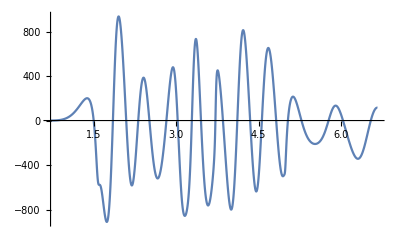

```mathematica
(*Grafico della gittata del proiettile nella configurazione appena trovata con la terza ottimizzazione*)
Plot[FG,{t,T1,T2},PlotRange->All,GridLines->{{Topt1,Topt2},{Gmax,Gmin}},GridLinesStyle->Directive[Orange,Dashed]]
```

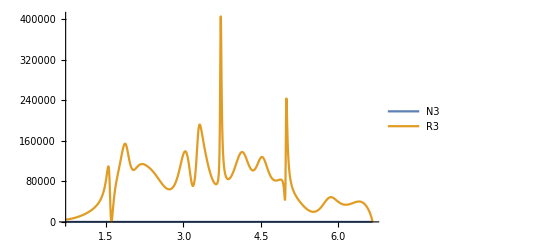

```mathematica
(*Grafico della normale del piano N3 e della tensione della fune R3*)
{h,L,L1,L2,m2,L3}={h,L,L1,L2,m2,L3}/.solM[[2]];
Plot[Evaluate[Simplify@Evaluate[{N3,R3}/.solR2]/.sol2],{t,T1,T2},PlotRange->All,PlotLegends->{"N3","R3"}]
```

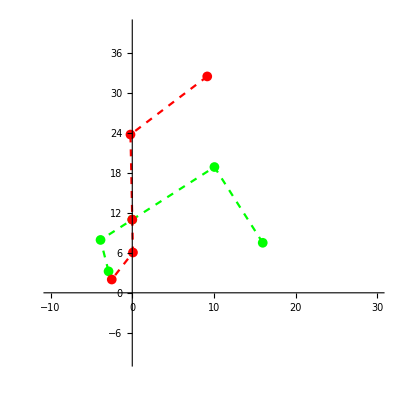

```mathematica
(*Grafico che mostra le configurazione nell'istante di lancio per la gittata massima verso destra (grafico verde) e la configurazione per la gittata massima verso sinistra (grafico rosso),dopo la terza ottimizzazione.
Questo grafico non varia con le ottimizzazioni successive*)
Show[ListLinePlot[{{xDt2[Topt1][[1]],yDt2[Topt1][[1]]},{xCt2[Topt1][[1]],yCt2[Topt1][[1]]},{xAt2[Topt1][[1]],yAt2[Topt1][[1]]},{xBt2[Topt1][[1]],yBt2[Topt1][[1]]},{xG2t2[Topt1][[1]],yG2t2[Topt1][[1]]}},PlotRange->{{-10,30},{-10,40}},AspectRatio->1,PlotMarkers->{"●",10},PlotStyle->{Dashed,Green}],ListLinePlot[{{xDt2[Topt2][[1]],yDt2[Topt2][[1]]},{xCt2[Topt2][[1]],yCt2[Topt2][[1]]},{xAt2[Topt2][[1]],yAt2[Topt2][[1]]},{xBt2[Topt2][[1]],yBt2[Topt2][[1]]},{xG2t2[Topt2][[1]],yG2t2[Topt2][[1]]}},PlotRange->{{-10,30},{-10,40}},AspectRatio->1,PlotMarkers->{"●",10},PlotStyle->{Dashed,Red}]]
```

```mathematica
(*Pulisco i parametri appena calcolati in questa ottimizzazione*)
Clear[h,L,L1,L2,m2,L3]
```

#### Ottimizzazione 4

```mathematica
(*Numero di iterazioni "i" e valori ottenuti a quel passo di iterazione*)
Row[{"i=",Dynamic[i]," Gmax(dx)=",Dynamic[Gmax]," Gmax(sx)=",Dynamic[Gmin]," T1=",Dynamic[T1]," T2=",Dynamic[T2]}]
```

i= Gmax(dx)= Gmax(sx)= T1= T2=

```mathematica
(*Grafico che mostra le configurazione nell'istante di lancio per la gittata massima verso destra (grafico verde) e la configurazione per la gittata massima verso sinistra (grafico rosso)*)
Dynamic@Show[ListLinePlot[Block[{t=Topt1},{{xDt2[t][[1]],yDt2[t][[1]]},{xCt2[t][[1]],yCt2[t][[1]]},{xAt2[t][[1]],yAt2[t][[1]]},{xBt2[t][[1]],yBt2[t][[1]]},{xG2t2[t][[1]],yG2t2[t][[1]]}}],PlotRange->{{-10,30},{-10,40}},AspectRatio->1,PlotMarkers->{"●",10},PlotStyle->{Dashed,Green}],ListLinePlot[Block[{t=Topt2},{{xDt2[t][[1]],yDt2[t][[1]]},{xCt2[t][[1]],yCt2[t][[1]]},{xAt2[t][[1]],yAt2[t][[1]]},{xBt2[t][[1]],yBt2[t][[1]]},{xG2t2[t][[1]],yG2t2[t][[1]]}}],PlotRange->{{-10,30},{-10,40}},AspectRatio->1,PlotMarkers->{"●",10},PlotStyle->{Dashed,Red}]]
```

```mathematica
solM=NMinimize[{
F[h,L,L1,L2,m2,L3],
10<h<13,
18<L< 22,
4<L1<6,
4<L2<6,
10000<m2<12000,
12<L3<15},{h,L,L1,L2,m2,L3},Method->{"NelderMead","PostProcess"->False}]
```

NMinimize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{-1094.88,{h→12.9735,L→21.9474,L1→5.972,L2→5.9492,m2→11991.5,L3→14.8368}}

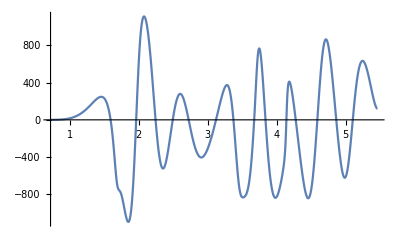

```mathematica
(*Grafico della gittata del proiettile nella configurazione appena trovata con la quarta ottimizzazione*)
Plot[FG,{t,T1,T2},PlotRange->All,GridLines->{{Topt1,Topt2},{Gmax,Gmin}},GridLinesStyle->Directive[Orange,Dashed]]
```

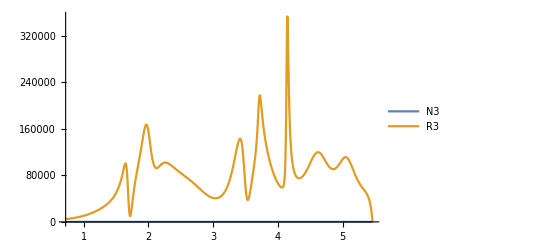

```mathematica
(*Grafico della normale del piano N3 e della tensione della fune R3*)
{h,L,L1,L2,m2,L3}={h,L,L1,L2,m2,L3}/.solM[[2]];
Plot[Evaluate[Simplify@Evaluate[{N3,R3}/.solR2]/.sol2],{t,T1,T2},PlotRange->All,PlotLegends->{"N3","R3"}]
```

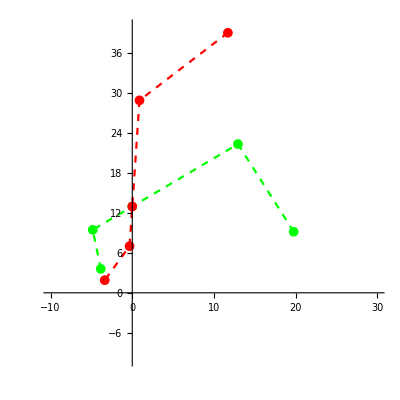

```mathematica
(*Grafico che mostra le configurazione nell'istante di lancio per la gittata massima verso destra (grafico verde) e la configurazione per la gittata massima verso sinistra (grafico rosso),dopo la quarta ottimizzazione *)
Show[ListLinePlot[{{xDt2[Topt1][[1]],yDt2[Topt1][[1]]},{xCt2[Topt1][[1]],yCt2[Topt1][[1]]},{xAt2[Topt1][[1]],yAt2[Topt1][[1]]},{xBt2[Topt1][[1]],yBt2[Topt1][[1]]},{xG2t2[Topt1][[1]],yG2t2[Topt1][[1]]}},PlotRange->{{-10,30},{-10,40}},AspectRatio->1,PlotMarkers->{"●",10},PlotStyle->{Dashed,Green}],ListLinePlot[{{xDt2[Topt2][[1]],yDt2[Topt2][[1]]},{xCt2[Topt2][[1]],yCt2[Topt2][[1]]},{xAt2[Topt2][[1]],yAt2[Topt2][[1]]},{xBt2[Topt2][[1]],yBt2[Topt2][[1]]},{xG2t2[Topt2][[1]],yG2t2[Topt2][[1]]}},PlotRange->{{-10,30},{-10,40}},AspectRatio->1,PlotMarkers->{"●",10},PlotStyle->{Dashed,Red}]]
```

### d) Aggiustare gli intervalli di ricerca, più volte, fino a trovare una soluzione con gittata superiore a 800 m .

#### Configurazione iniziale dopo l’ultima ottimizzazione

```mathematica
(*Angolo θ3 nella fase 1*)
θ3[t_]:=ArcSin[(h+(-L+L1) Sin[q1[t]])/L3]
```

```mathematica
(*Posizioni dei punti del trabucco in funzione del tempo per la fase 1*)
xAt[t_]:=Evaluate[xA/.sol]
yAt[t_]:=Evaluate[yA/.sol]
xDt[t_]:=Evaluate[xD/.sol]
yDt[t_]:=Evaluate[yD/.sol]
xCt[t_]:=Evaluate[xC/.sol]
yCt[t_]:=Evaluate[yC/.sol]
xBt[t_]:=Evaluate[xB/.sol]
yBt[t_]:=Evaluate[yB/.sol]
xG2t[t_]:=Evaluate[xG2/.sol]
yG2t[t_]:=Evaluate[yG2/.sol]
```

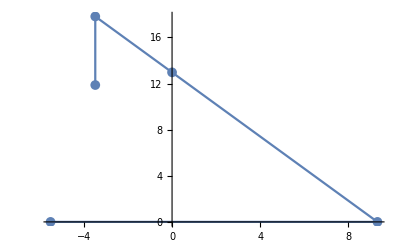

```mathematica
(*Configurazione iniziale all'istante t=0 dopo l'ultima ottimizzazione*)
ListLinePlot[{{xDt[0][[1]],yDt[0][[1]]},{xCt[0][[1]],yCt[0][[1]]},{xAt[0][[1]],yAt[0][[1]]},{xBt[0][[1]],yBt[0][[1]]},{xG2t[0][[1]],yG2t[0][[1]]}},PlotMarkers->{"●",10},PlotRange->All]
```

```mathematica
(*Ridefinisco il terzo grado di libertà*)
θ3[t_]:=q3[t]
```

#### Risultati ottenuti dopo l’ultima ottimizzazione

```mathematica
(*Gittata massima verso destra*)
Gmax
```

{247.047,{t→1.45738}}

```mathematica
(*Gittata massima verso sinistra*)
Gmin
```

{-1094.88,{t→1.84973}}

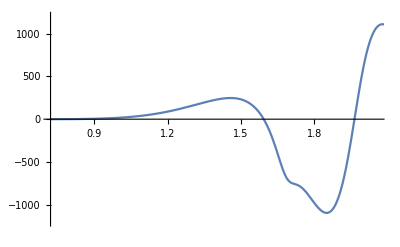

```mathematica
(*Grafico della gittata del proiettile nella configurazione finale*)
Plot[FG,{t,T1,T2},PlotRange->{{T1,Topt1+0.6},{-1200,1200}},GridLines->{{Topt1,Topt2},{Gmax,Gmin}},GridLinesStyle->Directive[Orange,Dashed]]
```

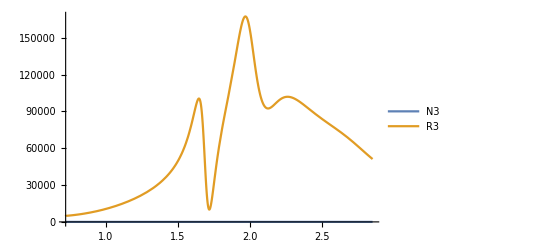

```mathematica
(*Grafico della normale del piano N3 e della tensione della fune R3 nella configurazione finale*)
Plot[Evaluate[Simplify@Evaluate[{N3,R3}/.solR2]/.sol2],{t,T1,Topt2+1},PlotRange->All,PlotLegends->{"N3","R3"}]
```

#### Animazione del trabucco

```mathematica
(*Animazione che mostra le configurazioni nell'istante di lancio per la gittata massima verso destra (grafico verde) e la configurazione per la gittata massima verso sinistra (grafico rosso).
In blu mostra il movimento del trabucco dopo l'ultima ottimizzazione*)
Animate[Show[ListLinePlot[Block[{t=Topt1},{{xDt2[t][[1]],yDt2[t][[1]]},{xCt2[t][[1]],yCt2[t][[1]]},{xAt2[t][[1]],yAt2[t][[1]]},{xBt2[t][[1]],yBt2[t][[1]]},{xG2t2[t][[1]],yG2t2[t][[1]]}}],PlotRange->{{-10,30},{-10,40}},AspectRatio->1,PlotMarkers->{"●",10},PlotStyle->{Dashed,Green}],ListLinePlot[Block[{t=Topt2},{{xDt2[t][[1]],yDt2[t][[1]]},{xCt2[t][[1]],yCt2[t][[1]]},{xAt2[t][[1]],yAt2[t][[1]]},{xBt2[t][[1]],yBt2[t][[1]]},{xG2t2[t][[1]],yG2t2[t][[1]]}}],PlotRange->{{-10,30},{-10,40}},AspectRatio->1,PlotMarkers->{"●",10},PlotStyle->{Dashed,Red}],ListLinePlot[{{xDt2[t][[1]],yDt2[t][[1]]},{xCt2[t][[1]],yCt2[t][[1]]},{xAt2[t][[1]],yAt2[t][[1]]},{xBt2[t][[1]],yBt2[t][[1]]},{xG2t2[t][[1]],yG2t2[t][[1]]}},PlotRange->{{-10,30},{-10,40}},AspectRatio->1,PlotMarkers->{"●",10}]],{t,T1,Topt2+1}]
```